```mathematica
caesar[str_,n_]:=StringReplace[str,MapThread[#1->#2&,{Alphabet[],RotateLeft[Alphabet[],n]}]]
```

```mathematica
caesar["ahoj",3]
```

dkrm

```mathematica
decaesar[str_]:=Table[caesar[str,n],{n,1,25}]
```

```mathematica
decaesar["egdbdueq"]
```

{fhecevfr,gifdfwgs,hjgegxht,ikhfhyiu,jligizjv,kmjhjakw,lnkikblx,moljlcmy,npmkmdnz,oqnlneoa,promofpb,qspnpgqc,rtqoqhrd,surprise,tvsqsjtf,uwtrtkug,vxusulvh,wyvtvmwi,xzwuwnxj,yaxvxoyk,zbywypzl,aczxzqam,bdayarbn,cebzbsco,dfcactdp}

```mathematica
"surprise"
```

{{1,2},{6,10549},{3,923},{7,13989},{8,14583},{9,13160},{5,6789},{10,10624},{11,7532},{4,3484},{12,4949},{13,2935},{14,1508},{16,324},{2,118},{15,784},{17,167},{20,10},{19,21},{18,60},{22,3},{21,3},{23,1}}

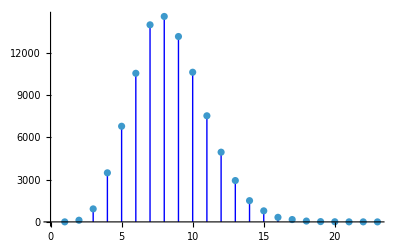

```mathematica
cetnosti=Tally[Map[StringLength[#]&,DictionaryLookup[]]]
ListPlot[cetnosti,Filling->Axis,FillingStyle->Blue]
```

```mathematica
N[Sum[cetnosti[[i,2]]*cetnosti[[i,1]],{i,1,23}]/Sum[cetnosti[[i,2]],{i,1,23}]]
```

8.39372

```mathematica
Select[DictionaryLookup[],StringLength[#]==23&]
```

{electroencephalographic}

```mathematica
Select[DictionaryLookup[],StringCount[#,{"a"|"e"|"i"|"o"|"u"}]>=9&]
```

{Andrianampoinimerina,bureaucratization,counterrevolutionaries,counterrevolutionary,denationalization,electroencephalographic,individualization,institutionalization,interdenominational,internationalization,overspecialization,professionalization,reinitialization,renationalisation}

```mathematica
Select[DictionaryLookup[],SubsetQ[{"A","E","F","H","I","K","L","M","N","T","V","W","X","Y","Z"},Characters[ToUpperCase[#]]]&]
```

{a,aah,Aaliyah,affiliate,affine,affinity,affix,aflame,aft,ah,aha,ahem,Aiken,ail,Aileen,ailment,aim,Aimee,aka,akin,Akita,Alan,Alana,alanine,ale,alewife,Alex,Alexei,alfalfa,Alhena,Ali,alien,alienate,alike,aliment,Aline,alive,aliyah,alkali,alkaline,alkalinity,alkalize,all,Allah,Allan,allay,allele,Allen,alleviate,alley,alleyway,Allie,ally,Alma,Almaty,Alnilam,Alnitak,Alta,Altai,Althea,Altman,Alva,Alvin,am,AM,Amalia,Amati,amaze,amazement,Amelia,amen,Amen,amenity,Amie,amine,amity,Amman,Amway,Amy,an,Ana,Anaheim,anal,anally,analyze,anathema,anathematize,anemia,anent,anew,aniline,animal,animate,Anita,ankh,ankle,anklet,Ann,Anna,annal,Annam,Anne,anneal,Annette,annex,annexe,Annie,annihilate,ant,ante,antenatal,antenna,antennae,anthem,anthill,anti,Antietam,Antillean,antitank,antivenin,Antwan,anvil,anxiety,any,anytime,anyway,at,Atalanta,ataxia,ate,Athena,Athene,Athenian,athlete,atilt,Atlanta,Atman,attain,attainment,attentive,attentively,Attila,Attlee,Ava,avail,Ave,Aventine,avian,Avila,await,awake,awaken,away,awe,awhile,awl,awn,ax,axe,Axel,axeman,axial,axially,axle,ayah,Ayala,aye,azalea,Azana,Azania,Azazel,AZT,Aztlan,eat,eaten,eave,eek,eel,eff,effeminate,effeminately,effete,effetely,Effie,eh,Eiffel,Eileen,eke,Elaine,Elam,elan,elate,element,elemental,elementally,Elena,elevate,eleven,eleventh,elf,elfin,Eli,Elia,eliminate,elite,Eliza,elk,ell,Ella,Ellen,Ellie,elm,Elma,Elnath,Eltanin,Elva,elven,Elvia,Elvin,Ely,em,email,emanate,Emil,Emile,Emilia,Emily,eminent,eminently,emit,Emma,Emmett,Emmy,en,enamel,enema,enemy,Enif,enliven,enlivenment,enmity,entail,entailment,entente,entitle,entitlement,entity,entwine,envy,enzyme,ET,eta,Ethan,ethane,Ethel,ethyl,ethylene,Etna,Etta,Eva,Evan,eve,Eve,Evelyn,even,Evenki,evenly,event,Evian,evil,evilly,Evita,ewe,ex,exalt,exam,examine,exhale,exile,exit,extant,extent,eye,eyelet,eyeteeth,Ezekiel,fa,faff,fail,faille,fain,faint,faintly,faith,Faith,fake,fall,fallen,Falwell,fame,familial,family,famine,fan,Fannie,fanny,Fanny,fantail,fanzine,fat,Fatah,fatal,fatality,fatally,fate,Fatima,fatten,fatty,fatwa,fave,fawn,fax,fay,Fay,Faye,faze,fealty,feat,fee,feel,feet,feint,feline,Felix,fell,fella,Fellini,felt,female,feminine,femininely,femininity,feminize,fen,Fenian,fennel,feta,fetal,fete,fettle,few,fey,Feynman,fez,Fez,Fianna,fiat,Fiat,fie,fief,fife,fifteen,fifteenth,fifth,fifthly,fiftieth,fifty,filament,file,filial,fill,fillet,filly,film,filmy,filth,filthily,filthy,fin,final,finale,finality,finalize,finally,fine,finely,finial,finite,finitely,fink,Finley,Finn,finny,fit,fitly,fitment,five,fix,fixate,fixative,fixity,fizz,fizzle,fizzy,flail,flak,flake,flaky,flam,flame,flan,flank,flannel,flannelet,flat,flatfeet,flatlet,flatly,flatmate,Flatt,flatten,flaw,flax,flaxen,flay,flea,flee,fleet,fleetly,Flem,flew,flex,flextime,flimflam,flint,Flint,flinty,flit,fly,flyaway,flyleaf,Flynn,flyway,flywheel,FM,FNMA,ha,Hafiz,haft,Hahn,Haifa,hail,Haiti,Haitian,hake,Hakka,Hal,halal,hale,Hale,Haleakala,Haley,half,halftime,halfway,halfwit,Halifax,halite,hall,Hall,Halley,Hallie,hallway,halt,halve,ham,Ham,Haman,Hamill,hamlet,Hamlet,Hamlin,Hammett,hammy,Han,Haney,hank,Hank,hankie,Hanna,Hannah,hat,hate,hath,Hathaway,Hattie,Havana,have,Havel,haven,haw,Haw,Hawaii,Hawaiian,hawk,hay,Hay,haywain,haze,hazel,Hazel,hazily,Hazlitt,hazy,he,heal,health,healthily,healthy,heat,heath,Heath,heathen,heatwave,heave,heaven,heavenly,heavily,heavy,heehaw,heel,heft,heftily,hefty,Heifetz,Heine,Heineken,Heinlein,Heinz,Helen,Helena,Helene,helix,hell,Hellene,Hellenize,Hellman,helm,helmet,helve,Helvetian,hem,hematite,heme,hemline,hen,Henley,henna,Hettie,hew,Hewitt,Hewlett,hex,hexane,hey,Hezekiah,hi,Hialeah,Hiawatha,hie,hike,hill,Hill,Hillel,hilly,hilt,him,Himalaya,Himalayan,Hinayana,hint,hit,Hittite,HIV,hive,hiya,hm,HTML,hyena,hymen,Hymen,hymeneal,Hymie,hymn,hymnal,I,Ian,if,iffy,Ike,Ila,ilea,Ilene,ilia,ilk,ill,ilmenite,imam,IMF,imitate,imitative,imitatively,immanent,immanently,imminent,imminently,in,Ina,inane,inanely,inanimate,inanimately,inanity,inattentive,inattentively,Inez,infamy,infant,infantile,infill,infinite,infinitely,infinitival,infinitive,infinity,infix,inflame,inflate,inhalant,inhale,initial,initialize,initially,initiate,initiative,ink,inkwell,inky,inlay,inlet,inmate,inn,innate,innately,innit,intake,Intel,intent,intently,inti,intimate,intimately,invent,inventive,inventively,invite,invitee,it,IT,Italian,Italianate,Italy,item,itemize,Iva,Ivan,ivy,Ivy,Izaak,Izanami,Kafka,Kaitlin,kale,Kalevala,Kali,Kalmyk,Kama,Kamehameha,kamikaze,Kan,Kane,Kant,Kantian,Kate,Katelyn,Kathie,Kathleen,Kathy,Katie,Katina,Katmai,Katy,Kay,kayak,Kaye,Kayla,Kazakh,Kazan,Kean,keel,keen,Keenan,keenly,Keewatin,Keith,Kelley,Kelli,Kellie,Kelly,kelvin,Kelvin,ken,Kennan,kennel,Kenneth,Kennith,Kenny,Kent,Kenya,Kenyan,Kenyatta,kettle,Keven,Kevin,key,Key,khaki,khan,Khan,Khayyam,kHz,Kiel,Kieth,Kiev,kill,kiln,kilt,Kim,kin,kine,kink,kinkily,kinky,Kinney,kit,Kit,kite,kith,kitten,kitty,Kitty,kiwi,Klan,Klee,Kleenex,Klein,Klimt,Kline,knave,knee,kneel,knell,knelt,knew,Knievel,knife,knit,kw,kW,Kwanzaa,kyle,Kyle,la,Lafayette,Lafitte,lain,laity,lake,lam,lama,Lamaze,lame,lamely,lament,lamina,laminae,laminate,LAN,Lana,lanai,Lanai,lane,Lane,lank,lankly,lanky,Lanny,late,lately,latent,latex,lath,lathe,Latin,Latina,latte,Latvia,Latvian,lav,lava,Laval,lave,law,Law,lawman,lawmen,lawn,lax,laxative,laxity,laxly,lay,layaway,layette,Layla,layman,laymen,laze,lazily,lazy,Le,lea,Lea,leaf,leaflet,leafy,Leah,leak,Leakey,leaky,lean,Lean,Leann,Leanna,Leanne,leave,leaven,lee,Lee,leek,leeway,left,Left,lefty,Lehman,lei,Leif,Leila,Lela,Lelia,lemma,lemme,Len,Lena,lenient,leniently,Lenin,lenitive,Lenny,lent,Lent,Lenten,lentil,let,Leta,Letha,lethal,lethality,lethally,Lethe,Letitia,Lev,Levant,levee,level,levelly,Levi,leviathan,Leviathan,Levine,levitate,Levitt,levity,levy,Levy,Lew,lexeme,lie,Lie,lief,lien,life,lifelike,lifeline,lifetime,lift,like,likely,liken,Lila,Lilia,Lilian,Liliana,Lilith,Lille,Lillian,Lillie,Lilly,lilt,lily,Lily,Lima,lime,limekiln,limey,limit,limn,limy,Lin,Lina,line,lineal,lineally,lineament,lineman,linemen,linen,liniment,link,linkman,linkmen,linnet,lint,lintel,linty,lit,litany,lite,lithe,lithely,little,Little,live,lively,liven,Livia,Livy,Liz,Liza,Lizzie,Lizzy,llama,Llewellyn,lye,Lyell,Lyle,Lyly,Lyman,Lyme,Lynette,Lynn,Lynne,Lynnette,lynx,LyX,ma,Mae,mafia,Mafia,mahatma,Mahayana,Mai,Maia,mail,mailman,mailmen,maim,Maiman,main,Maine,mainline,mainly,maintain,maize,make,Malawi,Malawian,Malay,Malaya,Malayalam,Malayan,male,Male,Mali,Malian,mall,mallet,malt,Malta,malty,mam,mama,Mamet,Mamie,mammal,mammalian,mammy,man,Man,Manama,manana,manatee,mane,Manet,Manhattan,Mani,mania,manikin,manila,Manila,manky,Manley,manlike,manly,Mann,manna,Mannheim,manta,mantel,mantilla,mantle,Mantle,Manx,many,mat,mate,matey,math,Mathew,matinee,Matt,matte,Mattel,Matthew,Mattie,maven,maw,Max,maxi,maxilla,maxillae,maxim,Maxim,maxima,maximal,maximality,maximally,Maximilian,maximize,Maxine,Maxwell,may,May,Maya,Mayan,mayfly,mayhem,Mazama,Mazatlan,maze,Mazzini,me,meal,mealtime,mealy,mean,meanie,meanly,meant,meantime,meanwhile,Meany,meat,meataxe,meaty,meek,meekly,meet,Mel,melamine,Melanie,melanin,melee,melt,Melva,Melville,Melvin,men,Menelik,menial,menially,meninx,Menkalinan,Menkent,Mennen,mental,mentality,mentally,met,Meta,metal,mete,methane,methyl,methylene,mettle,mew,mewl,mezzanine,mi,Mia,Miami,mien,miff,mike,Mike,Mikhail,mil,Milan,mile,militant,militantly,militate,militia,militiaman,militiamen,milk,Milken,milkman,milkmen,milky,mill,Mill,Millay,millennia,millennial,millet,Millet,Millie,Millikan,Milne,milt,mime,Mimi,mine,mini,minim,minima,minimal,minimality,minimally,minimize,minivan,mink,minke,Minna,Minnelli,Minnie,mint,Mintaka,minty,minx,MIT,mite,mitt,mitten,Mitty,Mitzi,mix,mizzen,my,myna,myth,nae,naff,NAFTA,nah,naif,nail,naive,naively,naivete,naivety,Nam,Namath,name,namely,nan,Nan,Nanak,Nanette,Nannie,nanny,Nat,natal,Natal,Natalia,Natalie,Nate,Nathan,Nathanael,Nathaniel,native,nativity,Nativity,nattily,natty,naval,nave,navel,navvy,navy,Navy,nay,Nazi,Neal,neat,neaten,neath,neatly,nee,Nehemiah,Neil,Nell,Nellie,Nelly,net,nett,Nettie,nettle,nevi,new,newel,newly,Newman,newt,next,NFL,NHL,Niamey,niff,niffy,niftily,nifty,Nike,Nikita,Nikkei,Nikki,nil,Nile,Nimitz,Nina,nine,nineteen,nineteenth,ninetieth,ninety,Nineveh,ninny,ninth,nit,Nita,nitwit,nix,Nixie,nth,ta,taffeta,taffy,Taft,Tahiti,Tahitian,tail,Tainan,Taine,taint,Taiwan,take,takeaway,taken,Taklamakan,tale,talent,tali,talk,talkative,talkatively,talkie,talky,tall,Talley,Tallinn,tally,tam,tamale,tame,Tameka,tamely,Tami,Tamika,Tamil,Tammany,Tammi,Tammie,Tammy,tan,Tana,Taney,Tania,tank,tannin,tantalize,Tanya,Tanzania,Tanzanian,tat,tatami,Tate,tattie,tattle,tattletale,tatty,Tawney,tawny,tax,taxi,taxiway,taxman,taxmen,tea,teak,teakettle,teal,team,teammate,teat,teatime,tee,teem,teen,teeny,teeth,teethe,tektite,Telemann,teletext,telex,tell,Tell,telltale,telly,ten,tenant,tenement,tenet,tent,tentative,tentatively,tenth,tenthly,Tet,Tevet,Tex,Texan,text,textile,Thai,thalami,Thalia,than,thane,Thanh,thank,Thant,that,thaw,the,Thea,thee,theft,Thelma,them,theme,then,theta,thew,they,thiamine,thief,thieve,thin,thine,think,thinly,thy,thyme,thymine,ti,Tia,tie,Tienanmen,tiff,Tiffany,til,tile,till,Tillman,tilt,Tim,time,timeline,timely,Timex,Timmy,tin,Tina,tine,tinkle,tinkly,tinnily,tinny,tint,tiny,titan,Titan,Titania,tithe,titian,Titian,titillate,titivate,title,tittle,titty,tizz,tizzy,TM,TNT,TV,TWA,twain,Twain,tweak,twee,tween,tweet,twelfth,twelve,twentieth,twenty,Twila,twilit,twill,twin,twine,twinkle,twinkly,twit,twixt,Ty,tyke,vain,vainly,Val,vale,Valenti,Valentin,valentine,Valentine,valet,Valhalla,valiant,valiantly,Valletta,valley,valve,van,Van,vane,vanilla,vanity,Vanzetti,vat,VAT,veal,vehement,vehemently,veil,vein,vela,Vela,Velez,Velma,Velveeta,velvet,velveteen,velvety,venal,venality,venally,venetian,Venetian,venial,Venn,vent,ventilate,vet,vex,vhf,VHF,via,vial,vie,Vienna,Vientiane,Vietminh,Vietnam,view,Vila,vile,vilely,vilify,villa,Villa,villain,villainy,ville,villein,villi,Vilma,vim,vine,vinyl,vita,vitae,vital,vitality,vitalize,vitally,vitamin,vitiate,Vitim,viva,Vivian,Vivienne,vivify,vixen,waffle,waft,waif,Waikiki,wail,wain,wait,Waite,waive,wake,Wake,waken,wale,walk,walkaway,Walkman,walkway,wall,Wall,walla,wallah,wallet,walleye,wally,Walt,waltz,wan,wane,wank,Wankel,wanly,wanna,want,watt,Watt,wattle,wave,Wave,wavelet,wavelike,wavily,wavy,wax,waxen,waxy,way,waylay,wayleave,Wayne,we,weak,weaken,weakly,weal,wealth,wealthy,wean,weave,wee,week,weekly,ween,weenie,weeny,weevil,weft,Wei,Weill,Weizmann,welkin,well,wellie,welly,welt,wen,went,wet,wetly,Wezen,whale,wham,whammy,what,wheal,wheat,wheaten,wheatmeal,whee,wheel,wheelie,wheeze,wheezily,wheezy,whelk,whelm,when,whet,whew,whey,whiff,while,whim,whine,whinny,whiny,whit,white,White,Whitehall,Whiteley,whitely,whiten,whitetail,whitewall,whitey,Whitley,Whitman,Whitney,whittle,whiz,why,wienie,wife,wifely,wile,Wiley,Wilhelm,Wilhelmina,Wilhelmine,will,Will,Willa,Willamette,William,willie,Willie,williwaw,willy,Willy,Wilma,wilt,wily,win,wine,wink,winkle,Winkle,Winnie,winy,wit,with,withal,withe,within,Witt,wittily,witty,wive,Wm,WWW,Wyatt,Wyeth,Wylie,Wynn,Xenia,xi,Xian,XL,XML,XXL,xylem,xylene,ya,Yahtzee,Yahweh,yak,Yakima,Yale,Yalta,yam,Yamaha,yank,Yank,Yankee,yaw,yawl,yawn,ye,yea,yeah,yell,Yemen,Yemeni,Yemenite,yen,yet,yeti,yew,yin,Yvette,Zane,zany,zeal,Zeke,Zelma,Zen,zenith,zeta,zine,zinnia,zit}

```mathematica
turtle[s_String,angle_,startdir_]:=Module[{dir=startdir,pos={0,0},path={{0,0}},left,right,i,ch=Characters[s]},left=RotationMatrix[angle];right=RotationMatrix[-angle];
Do[Which[ch[[i]]=="+",dir=left.dir,ch[[i]]=="-",dir=right.dir,ch[[i]]=="F",pos+=dir;AppendTo[path,pos]],{i,1,Length[ch]}];
ListLinePlot[path,Axes->False,AspectRatio->Automatic]]
```

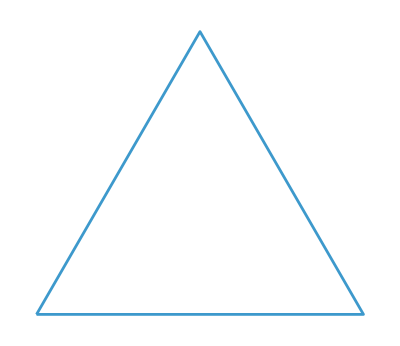

```mathematica
turtle["F++F++F",60 Degree,{1,0}]
```

```mathematica
"Rovnostranný trojúhelník"
```

```mathematica
genString[s_String,rule_,i_]:=Nest[StringReplace[#,rule]&,s,i]
```

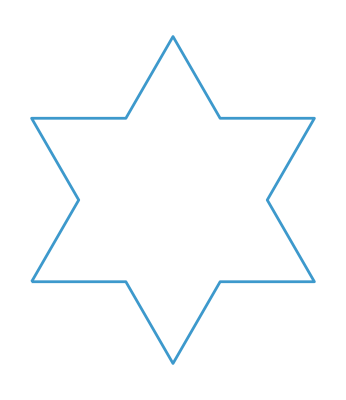

```mathematica
turtle[genString["F++F++F","F"->"F-F++F-F",1],60 Degree,{1,0}]
```

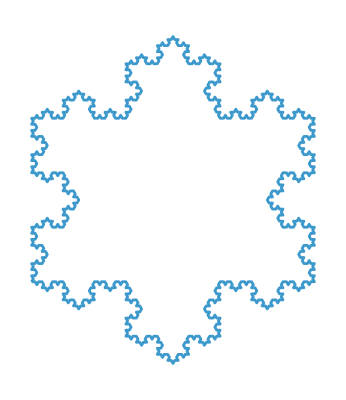

```mathematica
turtle[genString["F++F++F","F"->"F-F++F-F",4],60 Degree,{1,0}]
```

```mathematica
"Kochova vločka"
```

```mathematica
turtleNova[s_String,angle_,startdir_]:=Module[{dir=startdir,pos={0,0},path={{0,0}},left,right,i,ch=Characters[s],zasobnik={}},left=RotationMatrix[angle];
right=RotationMatrix[-angle];
Do[Which[ch[[i]]=="+",dir=left.dir,ch[[i]]=="-",dir=right.dir,ch[[i]]=="F",pos+=dir;AppendTo[path,pos],ch[[i]]=="[",AppendTo[zasobnik,{pos,dir}],ch[[i]]=="]",If[Length[zasobnik]>0,{pos,dir}=zasobnik[[-1]];
zasobnik=Most[zasobnik];
AppendTo[path,pos]]],{i,1,Length[ch]}];
ListLinePlot[path,Axes->False,AspectRatio->Automatic]]
```

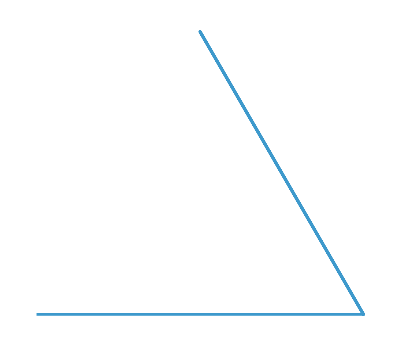

```mathematica
turtleNova["F++[F++]F",60 Degree,{1,0}]
```